# Data Analysis

Some data are imported from julia code https://github.com/djuliannader/RabiModel

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Figure 1

```mathematica
H[x_,p_,g_,λ_]=(p^2+x^2)/2-(1/2)*(1+(2^(1/2)*g*x+λ)^2)^(1/2);
```

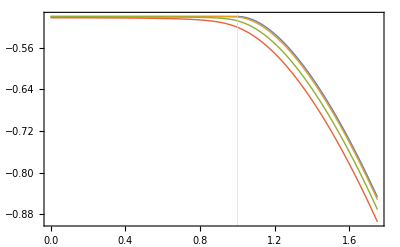

```mathematica
(*ground state energy as a function of g*)
GSQRM={};
GSAQRM1={};
GSAQRM2={};
GSAQRM3={};
ep=0.01;
Do[min=FindMinimum[H[x,0,gv,0],{x,-7,7}];
min1=FindMinimum[H[x,0,gv,0.01],{x,0,10}];
min2=FindMinimum[H[x,0,gv,0.05],{x,0,10}];
min3=FindMinimum[H[x,0,gv,0.1],{x,0,10}];
AppendTo[GSQRM,{gv,min[[1]]}];AppendTo[GSAQRM1,{gv,min1[[1]]}];
AppendTo[GSAQRM2,{gv,min2[[1]]}];
AppendTo[GSAQRM3,{gv,min3[[1]]}],{gv,0,1.75,ep}];

Evsg=ListPlot[{GSQRM,GSAQRM1,GSAQRM2,GSAQRM3},GridLines->{{1},{}},PlotStyle->Thick,GridLinesStyle->{{Thick,Black,Dashed},{}},Joined->True,Frame->True,LabelStyle->{Black,18}]
```

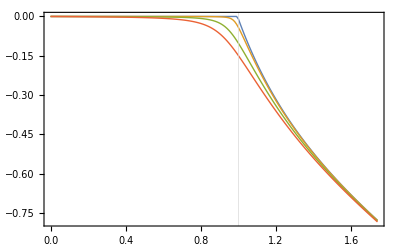

```mathematica
(*Derivative of the ground states energy as a function of g*)
DGSQRM={};
DGSAQRM1={};
DGSAQRM2={};
DGSAQRM3={};
Do[der=(GSQRM[[i+1,2]]-GSQRM[[i,2]])/ep;
der1=(GSAQRM1[[i+1,2]]-GSAQRM1[[i,2]])/ep;
der2=(GSAQRM2[[i+1,2]]-GSAQRM2[[i,2]])/ep;
der3=(GSAQRM3[[i+1,2]]-GSAQRM3[[i,2]])/ep;
AppendTo[DGSQRM,{GSQRM[[i,1]],der}];
AppendTo[DGSAQRM1,{GSAQRM1[[i,1]],der1}];
AppendTo[DGSAQRM2,{GSAQRM2[[i,1]],der2}];
AppendTo[DGSAQRM3,{GSAQRM3[[i,1]],der3}],{i,1,Length[GSQRM]-1}]

dEvsg=ListPlot[{DGSQRM,DGSAQRM1,DGSAQRM2,DGSAQRM3},Joined->True,PlotStyle->Thick,Frame->True,GridLines->{{1},{}},GridLinesStyle->{{Thick,Black,Dashed},{}},LabelStyle->{Black,18}]
```

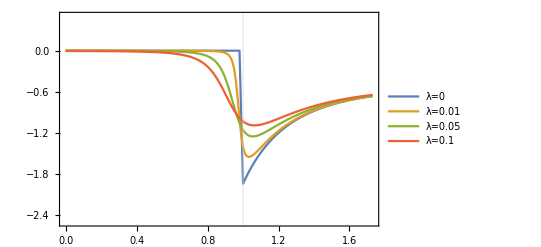

```mathematica
(*Second derivative of the ground states energy as a function of g*)D2GSQRM={};
D2GSAQRM1={};
D2GSAQRM2={};
D2GSAQRM3={};
Do[der=(DGSQRM[[i+1,2]]-DGSQRM[[i,2]])/ep;
der1=(DGSAQRM1[[i+1,2]]-DGSAQRM1[[i,2]])/ep;
der2=(DGSAQRM2[[i+1,2]]-DGSAQRM2[[i,2]])/ep;
der3=(DGSAQRM3[[i+1,2]]-DGSAQRM3[[i,2]])/ep;
AppendTo[D2GSQRM,{GSQRM[[i,1]],der}];
AppendTo[D2GSAQRM1,{GSAQRM1[[i,1]],der1}];
AppendTo[D2GSAQRM2,{GSAQRM2[[i,1]],der2}];
AppendTo[D2GSAQRM3,{GSAQRM3[[i,1]],der3}],{i,1,Length[DGSQRM]-1}]

d2Evsg=ListPlot[{D2GSQRM,D2GSAQRM1,D2GSAQRM2,D2GSAQRM3},PlotStyle->Thick,Joined->True,PlotRange->{All,{-2.5,0.5}},Frame->True,GridLines->{{1},{}},GridLinesStyle->{{Thick,Black,Dashed},{}},LabelStyle->{Black,18}]
```

## Figure 2

```mathematica
gt=0.75;
λt=0.0;
H[x_,p_,g_,λ_]=(p^2+x^2)/2-(1/2)*(1+(2^(1/2)*g*x+λ)^2)^(1/2);
FindMinimum[H[x,0,gt,λt],{x,-7,7}]
```

{-0.5,{x→-8.2931×10^-11}}

### Data

```mathematica
Ec1=-0.5;
Ec2=-0.550625;
Ec3=-0.5700940377221317;
datE0SQ1={{20,-0.48316775208226914},{30,-0.48883955833118153},{40,-0.491654029421549},{50,-0.4933353791002079},{60,-0.494453098205753},{70,-0.4952498697682969},{80,-0.49584655596449334},{90,-0.49630929959699505},{100,-0.49667980123202604}};
datE0SQ2={{20,-0.5326653116667086},{30,-0.5382134194102997},{40,-0.5412247128007457},{50,-0.5430686584686721},{60,-0.544309264694885},{70,-0.5452004204036267},{80,-0.5458714050865354},{90,-0.5463947902520856},{100,-0.5468144284435489}};
datE0SQ3={{20,-0.5508114634474034},{30,-0.5570711579540688},{40,-0.5602709687378027},{50,-0.5622103178570025},{60,-0.5635107750787274},{70,-0.5644432196969296},{80,-0.5651444356452189},{90,-0.5656909184046924},{100,-0.5661287815508436}};
datE0Q1={{10,-5.146947924790874},{20,-10.157004099708788},{30,-15.160796965487021},{40,-20.162795596159025},{50,-25.164030940258368},{60,-30.164870515456588},{70,-35.1654783837978},{80,-40.1659388891384},{90,-45.16629985081335},{100,-50.16659041002165}};
datE0Q2={{10,-5.700728683371035},{20,-11.14844030082671},{30,-16.643654532259983},{40,-22.14702806081865},{50,-27.651891728963918},{60,-33.157274492533745},{70,-38.66292302164267},{80,-44.16873047623011},{90,-49.67464107498637},{100,-55.18062247933808}};
datE0Q3={{10,-5.827407188450129},{20,-11.512498096551937},{30,-17.209860244728805},{40,-22.909187454246577},{50,-28.609205695399943},{60,-34.30954861015967},{70,-40.01007022080563},{80,-45.7107007268965},{90,-51.411402515529126},{100,-57.112153515949274}};
datdE1=Table[{datE0Q1[[i,1]],datE0Q1[[i,2]]/datE0Q1[[i,1]]},{i,1,Length[datE0Q1]}];
datdE2=Table[{datE0Q2[[i,1]],datE0Q2[[i,2]]/datE0Q2[[i,1]]},{i,1,Length[datE0Q2]}];
datdE3=Table[{datE0Q3[[i,1]],datE0Q3[[i,2]]/datE0Q3[[i,1]]},{i,1,Length[datE0Q3]}];
```

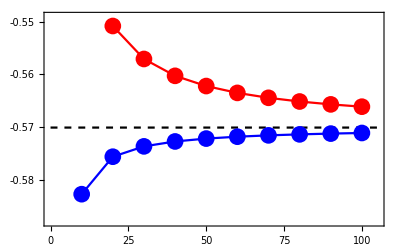

```mathematica
figdE=Show[ListPlot[{datdE3,datdE3,datE0SQ3,datE0SQ3},PlotRange->{{0,105},{-0.588,-0.549}},Joined->{True,False,False,True},FrameTicks->{{Range[-0.58,-0.55,0.01],None},{Automatic,None}},Frame->True,LabelStyle->{Black,20},PlotStyle->{Blue,{Blue,PointSize[0.03]},{Red,PointSize[0.03]},Red}],Plot[Ec3,{x,0,105},PlotStyle->{Black,Dashed}]]
```

## Figure 3

#### Wigner Function

```mathematica
(*Importing data from Julia*)
datawigner=Import["../../src/output/wigner_eig_data.dat"];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]:=Piecewise[{{RGBColor[1,(2 t)^6,(2 t)^6],0<=t<=1/2},{RGBColor[(2-2 t)^6,(2-2 t)^6,1],1/2<t<=1}}]
```

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datawigner,PlotRange->{{-1.25,1.25},{-1.25,1.25},All},Frame->True,LabelStyle->{Black,22},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-

#### Discrete Wigner function

```mathematica
(*Data from julia*)
M={{-0.0853075355878582,0.13906235077499315},{0.3609376492250067,0.1706150711757164}};
```

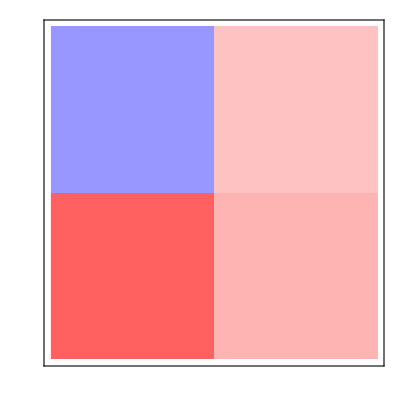

```mathematica
myColor[z_]:=Blend[{{-0.21,Blue},{0,White},{0.58,Red}},z]

figmat=MatrixPlot[M,ColorFunction->myColor,FrameTicks->None,ColorFunctionScaling->False,LabelStyle->{Black,12}(*,PlotLegends->Automatic*)]
```

## Figure 4

```mathematica
DataCor=Import["Data/Negativity_R50_sc.dat"];
data1a=Table[{DataCor[[i,1]],DataCor[[i,2]],DataCor[[i,3]]},{i,1,Length[DataCor]}];
data2a=Table[{DataCor[[i,1]],DataCor[[i,2]],DataCor[[i,4]]},{i,1,Length[DataCor]}];
data1b=Table[{DataCor[[i,1]],-DataCor[[i,2]],DataCor[[i,3]]},{i,1,Length[DataCor]}];
data2b=Table[{DataCor[[i,1]],-DataCor[[i,2]],DataCor[[i,4]]},{i,1,Length[DataCor]}];
data1=Join[data1a,data1b];
data2=Join[data2a,data2b];
```

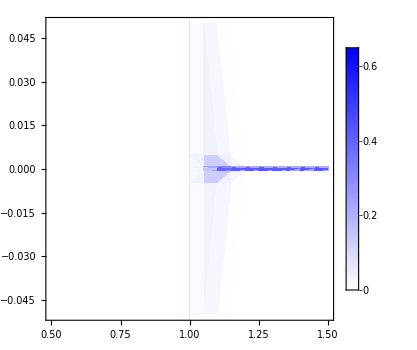

```mathematica
Clear[combinedData,colorFunction,densityPlot,blueScale,redScale,legends];

(* ========================================*)
(*1. Define independent color scales*)
(* ========================================*)

zmaxBlue=0.65;
zmaxRed=0.2;

(* ========================================*)
(*2. Combine datasets*)
(* ========================================*)

combinedData=MapThread[Function[{p1,p2},{p1[[1]],p1[[2]],p1[[3]]-p2[[3]]}],{data1,data2}];

(* ========================================*)
(*3. Define color function*)
(* ========================================*)

colorFunction[z_]:=Module[{intensity},If[z>=0,(*Positive difference:Blue*)intensity=Clip[z/zmaxBlue,{0,1}];
Blend[{White,Blue},intensity],(*Negative difference:Red*)intensity=Clip[Abs[z]/zmaxRed,{0,1}];
Blend[{White,Red},intensity]]];

(* ========================================*)
(*4. Create density plot*)
(* ========================================*)

densityPlot=ListDensityPlot[combinedData,ColorFunction->colorFunction,ColorFunctionScaling->False,InterpolationOrder->2,Mesh->None,GridLines->{{1},{}},GridLinesStyle->{{Thick,Black,Dashed},{}},PlotRange->{{0.5,1.5},{-0.05,0.05},All},AspectRatio->1,Frame->True,LabelStyle->{Black,20},ImageSize->350];

(* ========================================*)
(*5. Define independent legend scales*)
(* ========================================*)

blueScale=Blend[{White,Blue},Clip[#/zmaxBlue,{0,1}]]&;

redScale=Blend[{White,Red},Clip[#/zmaxRed,{0,1}]]&;

(* ========================================*)
(*6. Create two vertical color bars*)
(* ========================================*)

legends=Column[{BarLegend[{blueScale,{0,zmaxBlue}},LabelStyle->{Black,20},LegendMarkerSize->{20,150}],BarLegend[{redScale,{0,zmaxRed}},LabelStyle->{Black,20},LegendMarkerSize->{20,150}]},Spacings->2];

(* ========================================*)
(*7. Display figure*)
(* ========================================*)

ct=Legended[densityPlot,Placed[legends,Right]]
```

```mathematica
Export["Fig4f.png",ct];
```

## Figure 5

```mathematica
gt=1.5;
λt=0.05;
H[x_,p_,g_,λ_]=(p^2+x^2)/2-(1/2)*(1+(2^(1/2)*g*x+λ)^2)^(1/2);
NSolve[D[H[x,0,gt,λt],x]==0,x]
```

{{x→0.955692},{x→-0.944061},{x→-0.0424536}}

```mathematica
xmaxl=-0.04245364483397117;
```

```mathematica
datmar=Import["../../../GrossPitaevskiiSCF/src/marginalsx.dat"];
datmarx=Table[{datmar[[i,1]],datmar[[i,2]]},{i,1,Length[datmar]}];
```

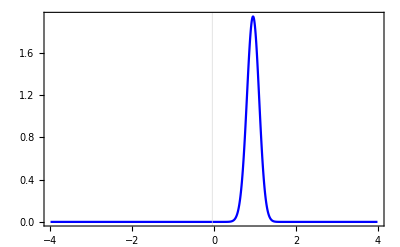

```mathematica
ListPlot[datmarx,Joined->True,PlotStyle->Blue,PlotRange->All,Frame->True,Axes->False,GridLines->{{xmaxl},{}},GridLinesStyle->{{Red,Thick},{}}]
```

```mathematica
First@MinimalBy[datmarx,Abs[#[[1]]-xmaxl]&];
pos=First@Ordering[Abs[datmarx[[All,1]]-xmaxl],1];
datmarx[[pos]];
```

```mathematica
Pl=Sum[datmarx[[i,2]]*(datmarx[[i+1,1]]-datmarx[[i,1]]),{i,1,pos}];
Pr=Sum[datmarx[[i,2]]*(datmarx[[i+1,1]]-datmarx[[i,1]]),{i,pos,Length[datmarx]-1}];
ratio=Pl/Pr
```

7.10432×10^-10

```mathematica
datLoc=Import["Data/Localization_R10.dat"];
datLoc1=Table[{datLoc[[i,1]],datLoc[[i,2]],datLoc[[i,3]]},{i,1,Length[datLoc]}];
datLoc2=Table[{datLoc[[i,1]],-datLoc[[i,2]],datLoc[[i,3]]},{i,1,Length[datLoc]}];
datLocP=Join[datLoc1,datLoc2];
```

```mathematica
L1={{1.0,0},{1.035,0.01},{1.046,0.015},{1.054,0.02},{1.063,0.025},{1.071,0.03},{1.080,0.035},{1.087,0.04},{1.094,0.045},{1.101,0.05}};
L2={{1.0,0},{1.035,-0.01},{1.046,-0.015},{1.054,-0.02},{1.063,-0.025},{1.071,-0.03},{1.080,-0.035},{1.087,-0.04},{1.094,-0.045},{1.101,-0.05}};
```

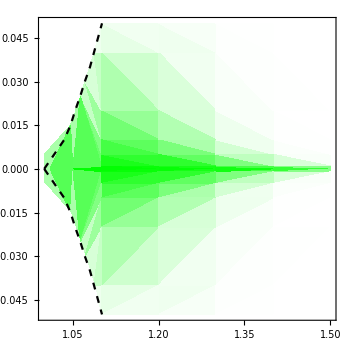

```mathematica
Show[ListDensityPlot[datLocP,ColorFunction->(Blend[{White,Green},#]&),Background->White,InterpolationOrder->2,Mesh->None,GridLines->{{},{}},PlotRange->{{1.0,1.5},{-0.05,0.05},{0,1}},AspectRatio->1,Frame->True,LabelStyle->{Black,14},ImageSize->350],ListPlot[{L1,L2},Joined->True,PlotStyle->{{Black,Dashed}}]]
```

## Figure 6

#### Potential

```mathematica
gt=1.2;
λt=0.0;
H[x_,p_,g_,λ_]=(p^2+x^2)/2-(1/2)*(1+(2^(1/2)*g*x+λ)^2)^(1/2);
FindMinimum[H[x,0,gt,λt],{x,-7,7}]
```

{-0.533611,{x→0.610567}}

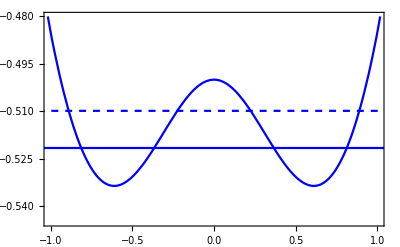

```mathematica
h0=-0.5408689711649409;
E0=-5.601223204434797/10;
Ecq=h0-(E0-h0);
Esc=-0.5098594927019168;
figpot=Show[Plot[H[x,0,gt,λt],{x,-1.25,1.25},PlotStyle->Blue,PlotRange->{{-1,1},{-0.545,-0.48}},Frame->True,LabelStyle->{Black,20},Axes->None],Plot[{Ecq,Esc},{x,-1.25,1.25},PlotStyle->{{Blue},{Blue,Dashed}}]]
```

#### Wigner Function

```mathematica
(*Importing data from Julia*)
datawigner=Import["../../src/output/wigner_eig_data.dat"];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]:=Piecewise[{{RGBColor[1,(2 t)^6,(2 t)^6],0<=t<=1/2},{RGBColor[(2-2 t)^6,(2-2 t)^6,1],1/2<t<=1}}]
```

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datawigner,PlotRange->{{-1,1},{-1,1},All},Frame->True,LabelStyle->{Black,22},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-

#### Discrete Wigner function

```mathematica
(*Data from julia*)
M={{0.0727094519351797,0.42729054806482003},{0.07270945193517998,0.42729054806482025}};
```

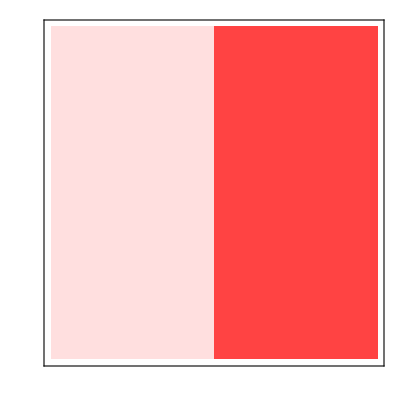

```mathematica
myColor[z_]:=Blend[{{-0.21,Blue},{0,White},{0.58,Red}},z]

figmat=MatrixPlot[M,ColorFunction->myColor,FrameTicks->None,ColorFunctionScaling->False,LabelStyle->{Black,12}(*,PlotLegends->Automatic*)]
```

## Figure 7

#### Wigner Function

```mathematica
(*Importing data from Julia*)
datawigner=Import["../../src/output/wigner_rhot_data.dat"];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datawigner,PlotRange->{{-1.25,1},{-1,1},All},Frame->True,LabelStyle->{Black,22},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-

#### Discrete Wigner function

```mathematica
(*Data from julia*)
M={{-0.08027429780031904,0.311270810146907},{0.5809897449983724,0.18801374265503995}};
```

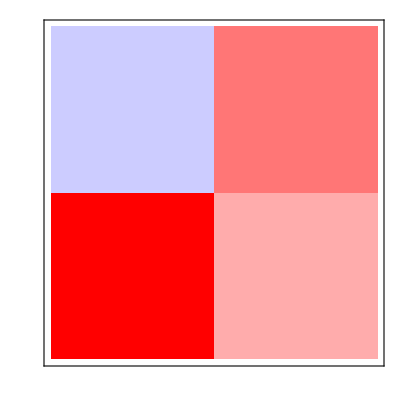

```mathematica
myColor[z_]:=Blend[{{-0.4,Blue},{0,White},{0.58,Red}},z]

figmat=MatrixPlot[M,ColorFunction->myColor,FrameTicks->None,ColorFunctionScaling->False,LabelStyle->{Black,12}(*,PlotLegends->Automatic*)]
```

#### Witnesses

```mathematica
dataNeg=Import["../../src/output/negativity_ramp.dat"];
datafid=Import["../../src/output/fidelities_ramp.dat"];
datamag=Import["../../src/output/magic_ramp.dat"];
datNegb=Table[{dataNeg[[i,1]],2*dataNeg[[i,3]]},{i,1,Length[dataNeg]}];
datfid1b=Table[{datafid[[i,1]],datafid[[i,2]]},{i,1,Length[datafid]}];
datfid2b=Table[{datafid[[i,1]],datafid[[i,3]]},{i,1,Length[datafid]}];
datPexb=Table[{datafid[[i,1]],datafid[[i,5]]},{i,1,Length[datafid]}];
datmanab=Table[{datamag[[i,1]],datamag[[i,2]]},{i,1,Length[datamag]}];
```

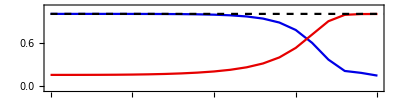

```mathematica
Show[ListPlot[{datfid1,datfid2},Joined->{True,True,True,True,False,False},Axes->False,Frame->True,PlotRange->{Automatic,{-0.05,1.1}},PlotStyle->{{Darker[Blue,0.1]},{Darker[Red,0.1]},{Darker[Blue,0.08],Dashed},{Darker[Red,0.08],Dashed},{Darker[Blue,0.08],Dotted},{Darker[Red,0.08],Dotted}},LabelStyle->{Black,10},GridLines->{{},{}},GridLinesStyle->{Red,{}}],Plot[1,{x,0,200},PlotStyle->{Black,Dashed}],AspectRatio->0.25]
```

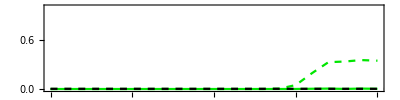

```mathematica
Show[ListPlot[{datNeg,datNegb},Joined->{True,True,False},Frame->True,Axes->False,PlotRange->{Automatic,{-0.01,1}},PlotStyle->{{Darker[Green,0.1]},{Darker[Green,0.1],Dashed},{Darker[Green,0.08]}},LabelStyle->{Black,10},GridLines->{{},{}},GridLinesStyle->{Red,{}}],Plot[{0.002474141963461518},{x,0,200},PlotStyle->{{Black,Dashed},{Black,Dashed}}],AspectRatio->0.25]
```

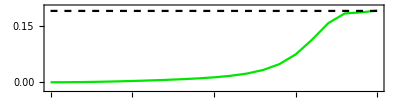

```mathematica
Show[ListPlot[{datmana},Joined->{True,True,False},Frame->True,Axes->False,PlotRange->{Automatic,{-0.02,0.2}},PlotStyle->{{Darker[Green,0.1]},{Darker[Green,0.1],Dashed},{Darker[Green,0.1]}},LabelStyle->{Black,10},GridLines->{{},{}},GridLinesStyle->{Red,{}}],Plot[{0.1887312732031543},{x,0,200},PlotStyle->{Black,Dashed}],AspectRatio->0.25]
```

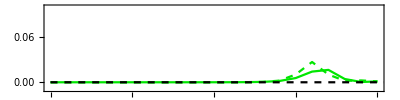

```mathematica
Show[ListPlot[{datPex,datPexb},Joined->{True,True,False},Frame->True,Axes->False,PlotRange->{Automatic,{-0.01,0.1}},PlotStyle->{{Darker[Green,0.1]},{Darker[Green,0.1],Dashed},{Darker[Green,0.1]}},LabelStyle->{Black,10},GridLines->{{},{}},GridLinesStyle->{Red,{}}],Plot[{0.0},{x,0,200},PlotStyle->{Black,Dashed}],AspectRatio->0.25]
```

## Figure 8

#### Continuous Wigner Function

```mathematica
(*Importing data from Julia*)
datawigner=Import["Data/ContinuousWigner_target_a.dat"];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]:=Piecewise[{{RGBColor[1,(2 t)^6,(2 t)^6],0<=t<=1/2},{RGBColor[(2-2 t)^6,(2-2 t)^6,1],1/2<t<=1}}]
```

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datawigner,PlotRange->{{-1,1},{-1,1},All},Frame->True,LabelStyle->{Black,22},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-

#### Discrete Wigner function

```mathematica
(*Data from julia*)
Datdw=Import["Data/DiscreteWigner_target_a.dat"];
datdw=Flatten[Datdw];
M={{datdw[[1]],datdw[[2]]},{datdw[[3]],datdw[[4]]}};
```

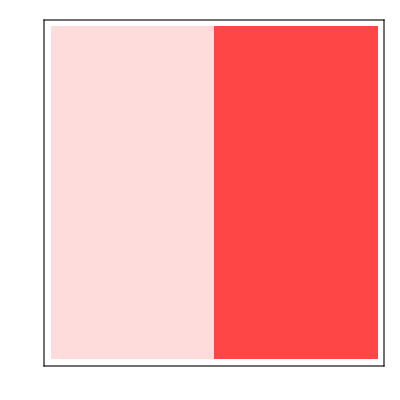

```mathematica
myColor[z_]:=Blend[{{-0.21,Blue},{0,White},{0.58,Red}},z]

figmat=MatrixPlot[M,ColorFunction->myColor,FrameTicks->None,ColorFunctionScaling->False,LabelStyle->{Black,12}(*,PlotLegends->Automatic*)]
```

#### FIdelity and negativity

```mathematica
dataFidvst=Import["Data/Fidelityvst_a.dat"];
dataNegvst=Import["Data/Negativityvst_a.dat"];
dataMagvst=Import["Data/Magicvst_a.dat"];
dataFidvstbl=Import["Data/Fidelityvst_a_kappa.dat"];
dataNegvstbl=Import["Data/Negativityvst_a_kappa.dat"];
dataMagvstbl=Import["Data/Magicvst_a_kappa.dat"];
```

```mathematica
fidtar=Table[{dataFidvst[[i,1]],dataFidvst[[i,3]]},{i,1,Length[dataFidvst]}];
fidinst=Table[{dataFidvst[[i,1]],dataFidvst[[i,5]]},{i,1,Length[dataFidvst]}];
fidneg=Table[{dataNegvst[[i,1]],2*dataNegvst[[i,3]]},{i,1,Length[dataNegvst]}];
fidmag=Table[{dataMagvst[[i,1]],dataMagvst[[i,2]]},{i,1,Length[dataMagvst]}];
fidtarbl=Table[{dataFidvstbl[[i,1]],dataFidvstbl[[i,3]]},{i,1,Length[dataFidvstbl]}];
fidinstbl=Table[{dataFidvstbl[[i,1]],dataFidvstbl[[i,5]]},{i,1,Length[dataFidvstbl]}];
fidnegbl=Table[{dataNegvstbl[[i,1]],2*dataNegvstbl[[i,3]]},{i,1,Length[dataNegvstbl]}];
fidmagbl=Table[{dataMagvstbl[[i,1]],dataMagvstbl[[i,2]]},{i,1,Length[dataMagvstbl]}];
```

```mathematica
gf=1.25;
T=50;
tc=T/π*ArcCos[1-2/gf];
```

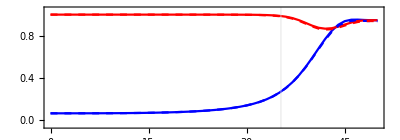

```mathematica
mainf=ListPlot[{fidtar,fidinst,fidtarbl,fidinstbl},PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed}},Joined->True,GridLines->{{tc},{}},GridLinesStyle->{{Black,Thickness[0.007]},{}},PlotRange->{{0,50},{-0.05,1.05}},Frame->True,LabelStyle->{Black,14},AspectRatio->0.35]
```

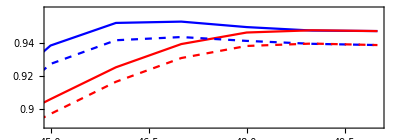

```mathematica
insetf=ListPlot[{fidtar,fidinst,fidtarbl,fidinstbl},PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed}},Joined->True,GridLines->{{tc},{}},GridLinesStyle->{{Black,Thick},{}},PlotRange->{{45,50},{0.89,0.96}},FrameTicks->{{{0.90,0.92,0.94},None},{Automatic,None}},Frame->True,LabelStyle->{Black,10},AspectRatio->0.35]
```

```mathematica
Show[mainf,Epilog->{Inset[Show[insetf,ImageSize->{140,100},Frame->True],Scaled[{0.3,0.6}]],Black,AbsoluteThickness[1.5]}]
```

-Graphics-

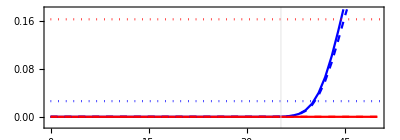

```mathematica
Show[ListPlot[{fidneg,fidmag,fidnegbl,fidmagbl},PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed}},PlotRange->{{0,50},{-0.015,0.18}},Joined->True,GridLines->{{tc},{}},GridLinesStyle->{{Black,Thickness[0.007]},{}},Frame->True,LabelStyle->{Black,14},AspectRatio->0.35],Plot[0.026253269393613023,{x,0,100},PlotStyle->{{Blue,Dotted}}],Plot[0.16331228714581192,{x,0,100},PlotStyle->{{Red,Dotted}}]]
```

## Figure 9

```mathematica
dataFidvsT=Import["Data/IndicatorsvsTperiod_a.dat"];
```

```mathematica
fidvsTper=Table[{dataFidvsT[[i,1]],dataFidvsT[[i,2]]},{i,1,Length[dataFidvsT]}];
fidvsTperbl=Table[{dataFidvsT[[i,1]],dataFidvsT[[i,3]]},{i,1,Length[dataFidvsT]}];
cnegvsTper=Table[{dataFidvsT[[i,1]],dataFidvsT[[i,4]]},{i,1,Length[dataFidvsT]}];
cnegvsTperbl=Table[{dataFidvsT[[i,1]],dataFidvsT[[i,5]]},{i,1,Length[dataFidvsT]}];
dnegvsTper=Table[{dataFidvsT[[i,1]],dataFidvsT[[i,6]]},{i,1,Length[dataFidvsT]}];
dnegvsTperbl=Table[{dataFidvsT[[i,1]],dataFidvsT[[i,7]]},{i,1,Length[dataFidvsT]}];
```

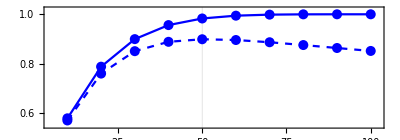

```mathematica
ListPlot[{fidvsTper,fidvsTper,fidvsTperbl,fidvsTperbl},PlotStyle->{{Blue},{Blue,PointSize[0.018]},{Blue,Dashed},{Blue,PointSize[0.018]}},Joined->{True,False,True,False},GridLines->{{50},{}},GridLinesStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->{{5,102},{0.55,1.02}},Frame->True,LabelStyle->{Black,14},AspectRatio->0.35]
```

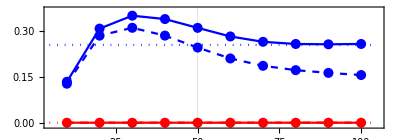

```mathematica
Show[ListPlot[{cnegvsTper,cnegvsTper,cnegvsTperbl,cnegvsTperbl,dnegvsTper,dnegvsTper,dnegvsTperbl,dnegvsTperbl},PlotStyle->{{Blue},{Blue,PointSize[0.018]},{Blue,Dashed},{Blue,PointSize[0.018]},{Red},{Red,PointSize[0.018]},{Red,Dashed},{Red}},Joined->{True,False,True,False},GridLines->{{50},{}},GridLinesStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->{{5,105},{-0.01,0.37}},Frame->True,LabelStyle->{Black,14},AspectRatio->0.35],Plot[0.25390634583782734,{x,0,105},PlotStyle->{{Blue,Dotted}}],Plot[0.0,{x,0,105},PlotStyle->{{Red,Dotted}}]]
```